```mathematica
NotebookEvaluate["~/Documents/Sparse\ Grids/Checking\ SBP/Methods\ and\ Functions\ for\ SBP.nb"]
```

```mathematica
Plot3D[#[x,y]-Sin[x+y],{x,0,1},{y,0,1}]&@project2D[Sin[#1+#2]&,3,3]
```

-Graphics3D-

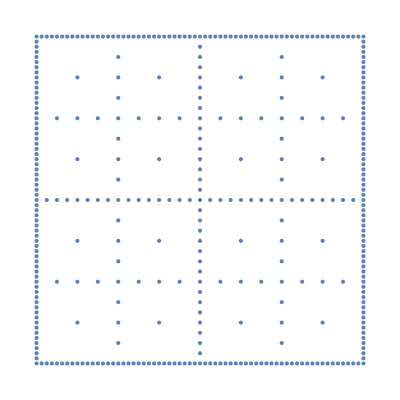

```mathematica
ListPlot[Flatten[makeSparse[6],3],Axes->False,AspectRatio->1]
```

```mathematica
(#+Transpose@#-lagrangedW[3,3])&@(dxMatrixStandard[3,3].lagrangeW[3,3])//MatrixPlot
```

-Graphics-

```mathematica
(#+Transpose@#-fulldW[3,3])&@(fullW[3,3].dxMatrix[3,3])//MatrixPlot
```

-Graphics-